```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[z]],Boxed->False,Axes->False,Background->RGBColor["#fdf6e3"]]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+2y^2),{x,-3,5},{y,-3,5},ColorFunction->Function[{x,y,z},Hue[z]],Boxed->False,Axes->False,Background->RGBColor["#fdf6e3"]]
```

-Graphics3D-

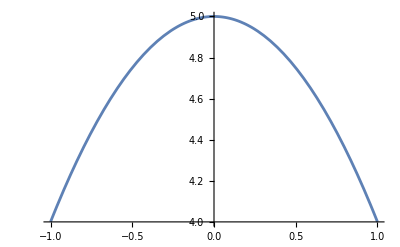

```mathematica
Plot[5-x^2,{x,-1,1}, Ticks->False ]
```

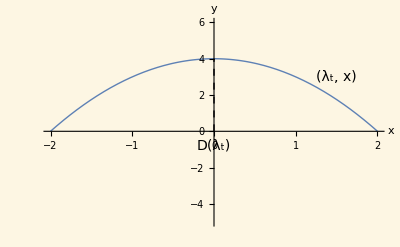

```mathematica
Plot[4-x^2,{x,-2,2},PlotRange->{-5,6},PlotStyle->Thick,Ticks->False,Axes->{True,False},
AxesLabel->{"x","y"},Ticks->{{{0,Style["D(λ)",Italic]},Automatic},Automatic},Epilog->{(*Vertical line at x=0*)Thick,Dashed,Line[{{0,0},{0,4}}],(*Label for the parabola*)Text[Style["(λ_t, x)",Italic,14],{1.5,3}],(*Label for the parabola*)Text[Style["D(λ_t)",Italic,14],{0,-0.8}]},Background->RGBColor["#fdf6e3"]]
```

```mathematica
NMaximize[{4-x^2-x-0.15x^3,-2<=x<=2},x]
```

{4.27289,{x→-0.574178}}

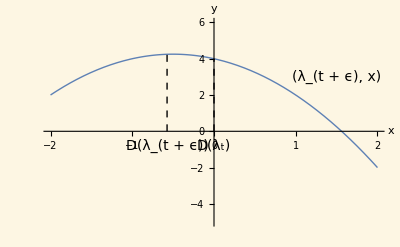

```mathematica
Plot[4-x^2-x,{x,-2,2},PlotRange->{-5,6},PlotStyle->Thick,Ticks->False,Axes->{True,False},
AxesLabel->{"x","y"},Ticks->{{{0,Style["D(λ_(t + ϵ))",Italic]},Automatic},Automatic},Epilog->{(*Vertical line at x=0*)Thick,Dashed,Line[{{0,0},{0,4}}],Thick,Dashed,Line[{{-0.5741781139483745,0},{-0.5741781139483745,4.272891907128432}}],(*Label for the parabola*)Text[Style["(λ_(t + ϵ), x)",Italic,14],{1.5,3}],(*Label for the parabola*)Text[Style["D(λ_t)",Italic,14],{0,-0.8}],Text[Style["D(λ_(t + ϵ))",Italic,14],{-0.5741781139483745,-0.8}]},Background->RGBColor["#fdf6e3"]]
```

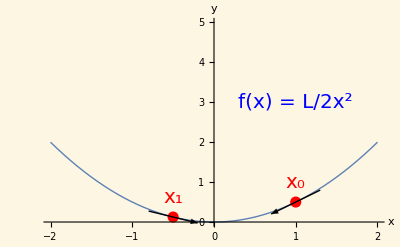

```mathematica
f[x_]:=x^2/2;

Plot[f[x],{x,-2,2},PlotStyle->Thick,PlotRange->{0,5},AxesLabel->{"x","y"},Epilog->{(*Points*)Red,PointSize[0.02],Point[{1,f[1]}],Point[{-1/2,f[-1/2]}],(*Labels*)Text[Style["x_0",20],{1,f[1]+0.5}],Text[Style["x_1",20],{-.5
,f[-1/2]+0.5}],(*Gradient arrows*)Black,Thick,Arrow[{{1+0.3,f[1]+0.3},{1-0.3,f[1]-0.3}}],Arrow[{{-1/2-0.3,f[-1/2]+0.5*0.3},{-1/2+0.3,f[-1/2]-0.5*0.3}}],Blue,Text[Style["f(x) = L/2x^2",20],{1,3}]},Background->RGBColor["#fdf6e3"]]
```

```mathematica
f[x_]:=x^2/2;

Plot[f[x],{x,-2,2},PlotStyle->Thick,PlotRange->{0,2},AxesLabel->{"x","y"},Epilog->{(*Points*)Red,PointSize[0.02],Point[{1,f[1]}],Point[{-1/2,f[-1/2]}],(*Labels*)Text[Style["(1, 1/2)",12],{1.2,f[1]+0.2}],Text[Style["(-1/2, 1/8)",12],{-0.9,f[-1/2]+0.2}],(
```